```mathematica
(*Começamos definindo a função a ser estudada*)
f[λ_][x_]:=x Exp[4λ(1-x)]
```

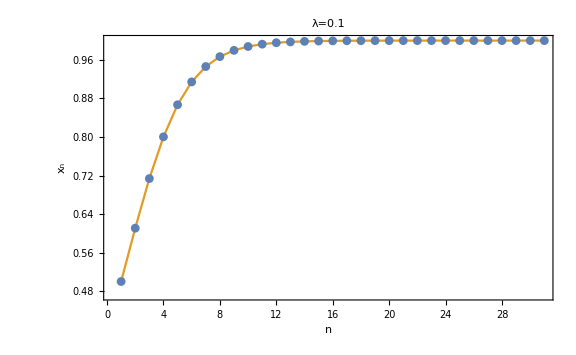

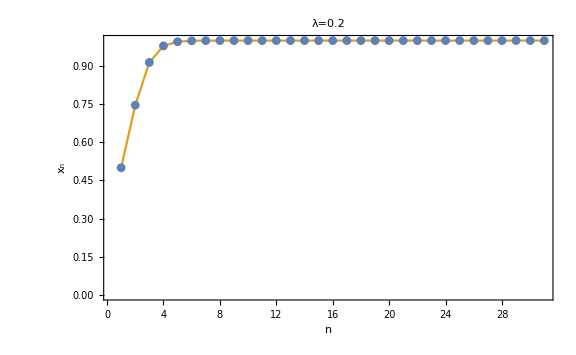

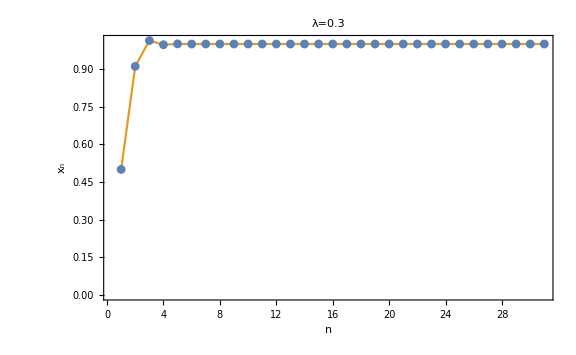

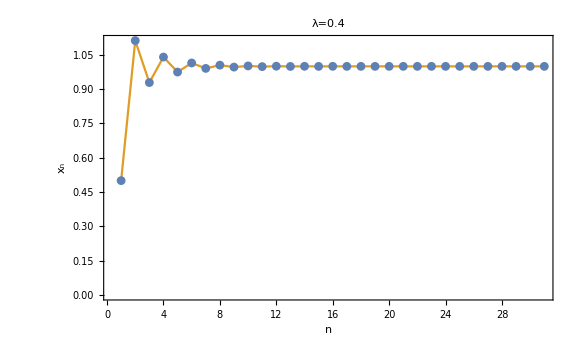

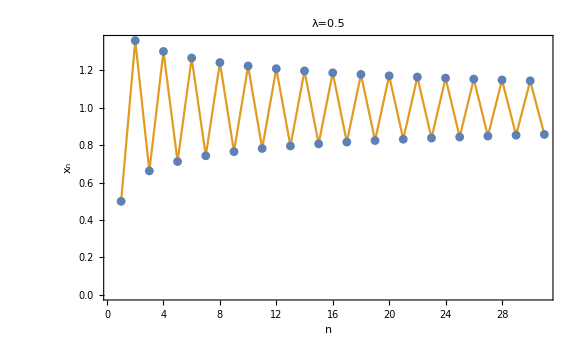

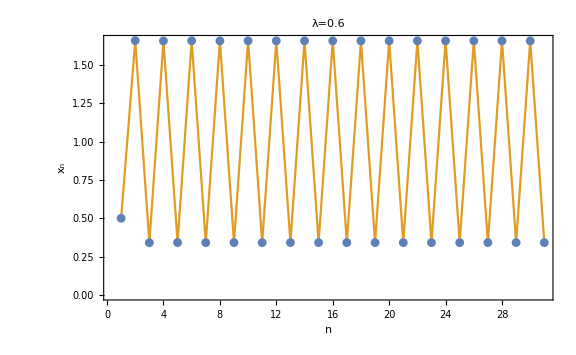

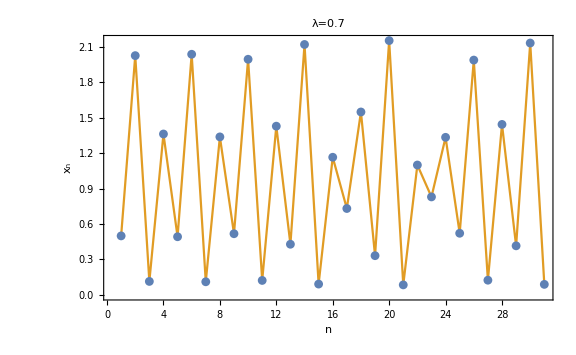

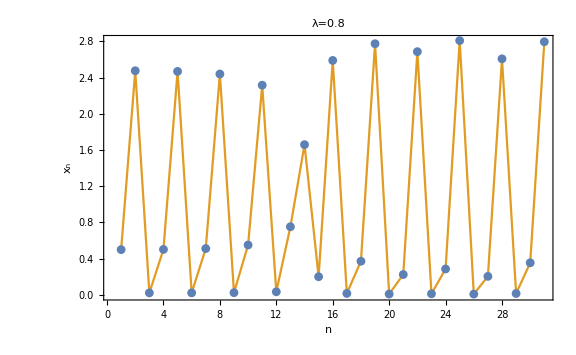

```mathematica
(*Faço testes empíricos de ponto fixo para diferentes valores de λ*)
lambda={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.95}; 
optam={ImageSize->Large,LabelStyle-> {"Large"}};
opgrf={Joined-> {False,True},Axes->False,Frame->True,FrameLabel->{"StyleBox[\"n\",FontSlant->\"Italic\"]","StyleBox[SubscriptBox[\"x\", \"n\"],FontSlant->\"Italic\"]"},PlotRange-> All,Evaluate[optam]};
Do[Print[ListPlot[{NestList[f[lambda[[i]]],1/2,30],NestList[f[lambda[[i]]],1/2,30]},PlotLabel->"λ="<>ToString[lambda[[i]]],Evaluate[opgrf]]],{i,1,Length[lambda]}]
```

```mathematica
(*Até λ aproximadamente igual a 0.5 é possível observar claramente a presença de um ponto fixo estável nos gráficos: x = 1. Para λ = 0.6 há alternância entre dois valores e, para λ = 0.7 em diante a identificação de qualquer padrão já se torna uma tarefa complicada. *)
```

```mathematica
(*O ponto fixo x = 1 foi o que apareceu mais frequentemente nos gráficos anteriores, sendo obtido para um intervalo considerável de parâmetros λ. De fato, ele é uma das soluções (reais) da equação f(x)=x *)
sol=Solve[f[λ][x]==x,x,Reals]
```

{{x→0},{x→1}}

```mathematica
(* Aparentemente ele é um ponto fixo válido para qualquer λ, mas façamos uma verificação de estabilidade mais específica com base na derivada de f:*)
Reduce[Abs[Simplify[D[f[λ][x],x]/.sol[[2]]]]<1,λ,Reals]
```

0<λ<1/2

```mathematica
(*Resultado que está em total acordo com os gráficos anteriores.*)
```

```mathematica
(*Utilizando o laço de repetição definido em aula, construo mapas de iteração para diferentes valores de λ, começando em x0 = 0.3*)
grafmapa[λ_,x0_,n_]:=
(xx=x0; (* Definimos uma variável auxiliar para aplicar o mapa *)
lista1={{xx,0},{xx,f[λ][xx]}}; (* Inicializamos a lista *)
Do[
( (* Começamos as instruções que serão repetidas no laço *)
xx=f[λ][xx];AppendTo[lista1,{xx,xx}];AppendTo[lista1,{xx,f[λ][xx]}]
),{i,1,n}  (* O laço é repetido n vezes *)
];(* Aqui se encerra o laço; abaixo fazemos os gráficos *)
grafico0=Plot[{x,f[λ][x]},{x,0,2},Evaluate[optam],AxesLabel->{"x","f(x)"}];
Show[{grafico0,ListLinePlot[lista1,PlotStyle->Red]}]
)
```

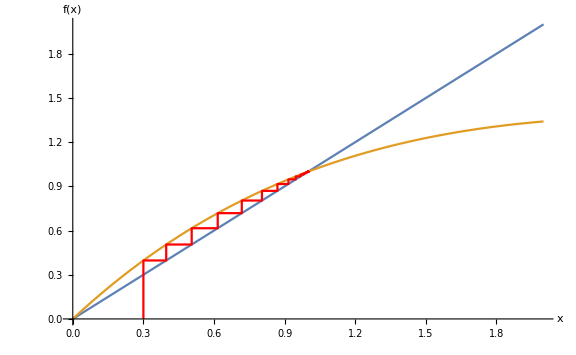

```mathematica
grafmapa[0.1,0.3,100]
```

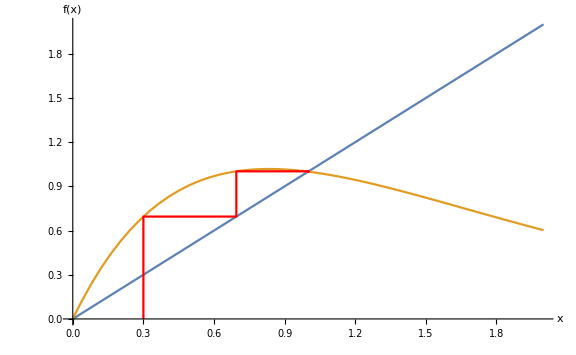

```mathematica
grafmapa[0.3,0.3,100]
```

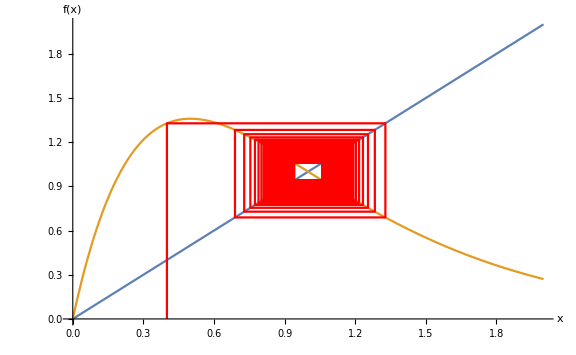

```mathematica
grafmapa[0.5,0.4,200]
```

```mathematica
grafmapa[0.6,0.3,400]
```

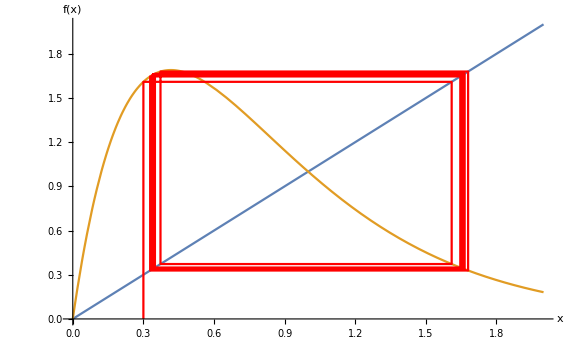

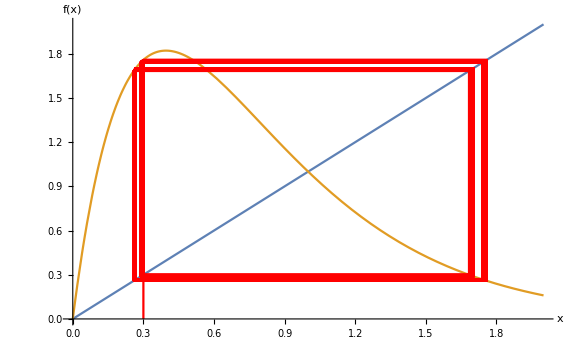

```mathematica
grafmapa[0.631617,0.3,300]
```

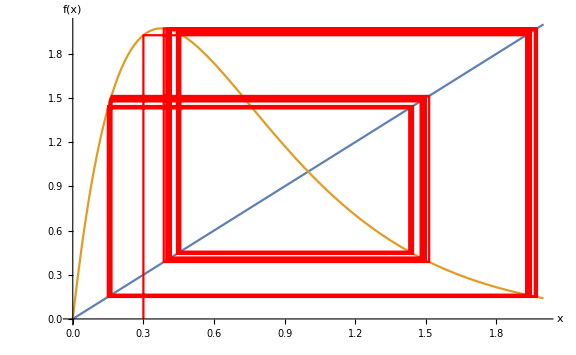

```mathematica
grafmapa[0.664088,0.3,100]
```

```mathematica
(*Até λ = 0.5 é possível observar o comportamento tendencioso para o ponto fixo x = 1 perfeitamente. Para λ = 0.6 o mapa apresenta um padrão de quadrilátero, indicando a alternância das iterações em 2 valores de x. Em particular, x = 0.35 e x = 1.65, aproximadamente.*)
```

```mathematica
(*Tento identificar a presença de ciclos 2. Verifico o caso λ = 0.6*)
sols2=NSolve[x==Nest[f[0.6],x,2],x,Reals]
```

{{x→0.},{x→0.34143},{x→1.},{x→1.65857}}

```mathematica
(*Note que, exceto os valores x = 0 e x = 1, que já eram pontos fixos iniciais, os resultados x = 0.34143 e x = 1.65857 são valores muito próximos das estimativas feitas empiricamente*)
```